```mathematica
ClearSystemCache[];
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
```

```mathematica
mn=0.939;(*GeV*)
G =  6.67408*^-11; (*Grav Constant*)
vd  = 200/cspeed;(* kms^-1/c *)
vn =  230 /cspeed;(* kms^-1 /c*)
cspeed=299792458;(*m/s*)
km=1000;(*km/m*)
cm=1/100;(*cm/m*)
Gevto1fm=1000/197.3;(*1/(GeV*fm)*)
fm1to1m=10^15;(*m/fm*)
ρχ = 0.4*(hbarc)^3*1*^6;  (*Gev^4*) 
hbarc = (0.1973269788*1.*^-15); (* GeV m *)
Prefactor=(1/cm)^3*(Gevto1fm^(-2))*fm1to1m*cspeed//Simplify;
ϵreg=10^(-4);
σSB = 5.67*^-8*6.582*^-25*(hbarc)^2/(1.60*^-10);
TT = 10^10*3.154*^7/6.58*^-25;
```

```mathematica
qp[q0_, Ek_, mx_] := √(2Ek mx) + √(2mx(Ek - q0));
qm[q0_, Ek_, mx_] := √(2Ek mx) - √(2mx(Ek - q0));
vr[Ek_, mx_]:= (mn +mx)/(mn mx)√(2mx Ek);
vperp[q_,Ek_,mx_]:= vr[Ek, mx] + (q(mx + mn))/(2(mx*mn));
prefactor[Ek_, mx_]:= 1/(64 π^3 mx √(2mx Ek));
```

## Neutron Star EoS

#### Load in data

```mathematica
EoSHeaders = Import["eos_24_lowmass.dat"];
Dataset[EoSHeaders[[1,All]]] (*Print out headings so I know what I'm doing *)
EoSData =Drop[EoSHeaders, 1] ;(* Remove Headings *)
```

Dataset[<>]

Make Interpolating Functions

```mathematica
radius = EoSData[[All,1]];

rMin = radius[[1]];
rMax = Rstar= 11.6;

μf[x_]:= Interpolation[ EoSData[[All, {1,8}]] ][x*Rstar]*1*^-3; (* Chemical potential in GeV *)

nb          = EoSData[[All,3]];
Yn          = EoSData[[All, 7]];
muList = EoSData[[All, 8]];

ndList = nb*Yn;
nprof=Interpolation[ Transpose[{radius,nb*Yn}]]; (* Neutron density in fm^-3*)

MNS = Interpolation[EoSData[[All, {1, 2}]]]; (* In units of M_⊙ *) 

p =Interpolation[EoSData[[All, {1, 12}]]]; (* in dyn/cm^2*)
```

```mathematica
EscVelSetUp[rad_?NumericQ] := Module[                                                           (* escape velocity inside star, in natural units *)
{GravPot,r}, 
GravPot =NIntegrate[(2.*G*MNS[r]*2.*^30)/(r^2*1.*^3), {r, rad, rMax}];
Sqrt[GravPot +(2.*G*MNS[rMax]*2.*^30)/(rMax*1.*^3)]/cspeed
]; 


ve = Interpolation[Table[{ri, EscVelSetUp[ri]}, {ri, rMin, Last[radius]}]];
```

```mathematica
(*Define Rstar, ζ0, B[r], nprof[r] (the true baryon density, NOT energy density) and μf[r].
Rstar in kmeters
nprof in the unit you want, I use fm^-3
ζ0 in the right unit to match nprof and nfree (That is in GeV^3)
μf in GeV
 IMPORTANT: definitions have to be functions that can be evaluated fast!*)
```

```mathematica
rtA[r_]:=Sqrt[1/(1 -(2*G*MNS[r*Rstar]*2*^30)/(r*Rstar*1*^3*cspeed^2))];
```

```mathematica
Clear[B];
B =NDSolveValue[{y'[x]==(2*G*(Rstar*1*^3))/(cspeed^2*(x*(Rstar*1*^3))^2)*((MNS[x*Rstar]*2*^30+p[x*Rstar]*0.1*(x*(Rstar*1*^3))^3/cspeed^2)/( 1 - (2*G*MNS[x*Rstar]*2*^30)/(cspeed^2*(x*(Rstar*1*^3)))))*y[x], y[1]==(1 - (2*G*MNS[1*Rstar]*2*^30)/(cspeed^2*(Rstar*1*^3)))},y, {x, rMin/Rstar, 1}];
(*takes as input r/Rstar (from 0 to 1)*)
```

```mathematica
ζ0=5.278368626202642(*Note that is not a problem that it is >1, as I use different units for ntrue and nfree, in same units result is 0.04*);
```

## Matrix Elements

```mathematica
MC[q_,Ek_,mx_]:=16 mx^2 mn^2;
Mq2[q_,Ek_,mx_]:= vperp[q, Ek, mx];

d1M[q_,Ek_,mx_]:=MC[q,Ek,mx];
d2M[q_,Ek_,mx_]:= 4 mn^2 q^2;
d3M[q_,Ek_,mx_]:=4 mx^2 q^2;
d4M[q_,Ek_,mx_]:= q^4;
d5M[q_,Ek_,mx_]:= MC[q,Ek,mx];
d6M[q_,Ek_,mx_]:= 8 mx^2*(mn^2*vperp[q, Ek, mx]^2+4 q^2);
d7M[q_,Ek_,mx_]:=8 mn^2*(mx^2*vperp[q, Ek, mx]^2+4 q^2);
d8M[q_,Ek_,mx_]:=12 mx^2 mn^2;
d9M[q_,Ek_,mx_]:=3 mx^2 mn^2;
```

## Interaction Rate

```mathematica
Γ[Ek_, M2_,mx_]:= prefactor[Ek, mx]*Integrate[q0*M2[q, Ek, mx],{q0, 0, Ek}, {q, qm [q0, Ek, mx], qp[q0, Ek, mx]}];
```

## Therm Time

```mathematica
denom[Ek_, M2_,mx_]:= prefactor[Ek, mx]*Integrate[q0^2*M2[q, Ek, mx],{q0, 0, Ek}, {q, qm [q0, Ek, mx], qp[q0, Ek, mx]}];
fracLost[Ek_, M2_,mx_]:=denom[Ek, M2, mx]/Γ[Ek, M2, mx];
```

```mathematica
ttnoΛ[E0_, Eth_,M2_, mx_]:=-Integrate[1/denom[Ek, M2, mx], {Ek, E0, Eth},GenerateConditions->False];
ttFull[E0_, Eth_, TH_, op_, mx_, Λ_]:=-Integrate[Λ[ToExpression[ToString[op]<>"CAP"], TH, mx]^4/denom[Ek, ToExpression[ToString[op]<>"M"], mx], {Ek, E0, Eth},GenerateConditions->False]*6.58*^-25*3.17098*^-8; (*in years*)
```

## Summation Therm

```mathematica
τ[E0_,M2_,mx_]:= (
Clear[Enow, time];
Enow = E0;
time =0;
While[ Enow > 8*^-9,
time +=1/Γ[Enow, M2, mx];
Enow += -fracLost[Enow, M2, mx];
];
Return[time];
Clear[Enow, time];
)
```

## Λ constraints from therm

```mathematica
Λ[M2_, T_, mx_]:= (TT/ttnoΛ[mx/3,T,M2, mx])^0.25;
```

## Capture Rates

### Geometric Limit

```mathematica
GeomLim[mχ_]:=Pi*(Rstar*km/hbarc)^2(1-B[1-ϵreg])/B[1-ϵreg]ρχ/mχ*Erf[Sqrt[3/2]vn/vd]/(vn*km);
```

### Full Rates

```mathematica
Do[
Evaluate[Symbol[cap<>"CAP"]] =Interpolation[Import[StringJoin[{"../cap_rate/Mathematica_cap/", cap, "_cap.dat"}]]]
,
{cap, {"d0", "d1", "d2","d3","d4","d5","d6","d7", "d8", "d9", "d10"}}
]
```

## Heating Functions

```mathematica
fracCAP[dCAP_, mx_]:=dCAP[Log10[mx]]/GeomLim[mx];
```

### Kinetic Heating

```mathematica
ΛKH[dCAP_,T_, mx_]:= 1570/T*(fracCAP[dCAP, mx])^(1/4);
```

### Annihilation Heating

```mathematica
ΛAH[dCAP_,T_, mx_]:= 2310/T*(fracCAP[dCAP, mx])^(1/4);
```

```mathematica
ttFull[1*^5/3, 1*^-9, 2310,  d4, 1*^5,ΛAH]
```

171.586

```mathematica
Do[
Clear[out];
out = With[
{x:=10^xp}, 
Table[
 Flatten[{x,Table[
ttFull[x/3, 1*^-9, TEMP, ToExpression[oper<>"M"], x, ΛAH, ToExpression[oper<>"CAP"]],
{TEMP, {100, 500, 1570, 2310}}
]}],
{xp, -4.8, 5, 0.1}]];
Export[oper<>"_annheat_tt.dat", out, "Table"]
,
{oper, {"d1","d2", "d3", "d4", "d5", "d6", "d7", "d8", "d9"}}
]

Do[
Clear[out];
out = With[
{x:=10^xp}, 
Table[
 Flatten[{x,Table[
ttFull[x/3, 1*^-9, TEMP, ToExpression[oper<>"M"], x, ΛKH, ToExpression[oper<>"CAP"]],
{TEMP, {100, 500, 1570}}
]}],
{xp, -4.8, 5, 0.1}]];
Export[oper<>"_kinheat_tt.dat", out, "Table"]
,
{oper, {"d1","d2", "d3", "d4", "d5", "d6", "d7", "d8", "d9"}}
]
```

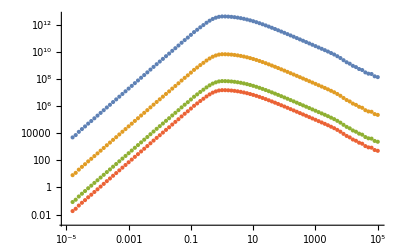

```mathematica
ListLogLogPlot[%]
```